## First Order Variation

Assignment: 
1. Generate Brownian motion simulations using both:
	A. Scaled random walk (based on independent Bernoulli random variables, e.g. coin tosses)
	B. Sampled Brownian motion based on Gaussian increments with the appropriate variance 
	(Hint: see RandomVariate and NormalDistribution functions)
2.  Write a function that computes the first order variation (FOV) of a given list of numbers.
3.  Apply to both scaled random walk (A) and to sampled Brownian motion (B), for 20 paths each (20 RW paths, 20 BM paths)
    i. For each simulated path, go from 0 to 10 seconds with 10 sample points per second, and plot the FOV at each time point.  Thus each plot should go from 0 to 10 seconds at 0.1 second increments.  
    ii. Which type of plot (RW vs BM) shows more variability and why?
4.  Show that FOV →∞ as the partition size ||Π||→0. (Hint: evaluate FOV for the number of points per unit time = 10, 100, 1000 and observe the FOVvalues)

Due Friday April 8th by Midnight.

## Question 1

{0,-√(2/11),0,-√(2/11),0,√(2/11),2 √(2/11),3 √(2/11),4 √(2/11),3 √(2/11),2 √(2/11),√(2/11)}

{0,-0.254221,-0.477049,-0.569003,-0.536073,-0.541378,-0.645317,-0.588075,-0.184197,-0.528034,-0.433911,-0.136998,-0.198812,-0.2294,-0.324582,-0.188537,-0.359089,-0.00143178,-0.0357492,-0.18954,-0.487516,-0.447228,-0.732853,-0.689242,-0.430818,-0.221309,-0.308344,-0.217812,-0.377653,-0.641032,-0.542583,-0.789767,-0.611849,-0.637216,-0.566005,-0.67831,-0.754237,-0.692854,-0.60945,-0.818686,-0.916433,-0.895363,-1.01891,-0.926263,-1.14778,-0.648444,-0.910943,-1.18039,-1.41988,-1.48288,-1.39357,-1.77932,-2.14892,-2.4134,-2.41854,-2.16189,-1.98946,-1.89228,-2.33515,-2.13286,-2.08592,-2.34839,-2.44767,-2.35596,-2.20092,-2.24964,-2.39673,-2.51988,-2.86797,-2.61226,-2.38456,-2.87481,-3.08213,-3.10028,-2.72595,-3.18145,-3.12971,-3.03626,-3.20499,-2.91864,-2.86675,-2.67358,-2.68297,-2.46073,-2.60873,-2.56772,-2.43946,-2.61432,-2.36438,-2.4515,-2.31393,-2.15725,-2.13725,-1.91786,-2.13945,-2.62643,-2.63211,-2.94057,-2.80565,-3.24489,-3.15886}

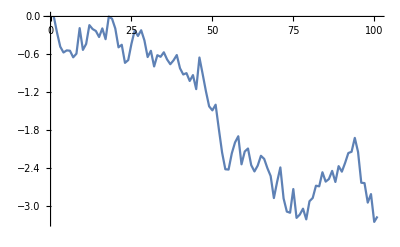

```mathematica
(*iSteps is total number of steps. iSteps = num_seconds * points_per_second*)

xScaledWalk[nSeconds_, iSteps_]:=Module[{vnSteps},
vnSteps=RandomChoice[{-1,1},iSteps];
vnSteps=vnSteps/Sqrt[iSteps/nSeconds];
FoldList[Plus,0,vnSteps]
];
xBrownianMotion[nSeconds_, iSteps_]:=Module[{vnSteps},
vnSteps=RandomVariate[NormalDistribution[0,Sqrt[nSeconds/iSteps]],iSteps];
FoldList[Plus,0,vnSteps]
];
vnRes=xScaledWalk[2,11];
vnRes
vnRes=xBrownianMotion[5,100];
vnRes
ListPlot[vnRes,Joined->True]
```

## Question 2

```mathematica
xFOV[nList_] := Module [{},
Total[Abs[Differences[nList]]]
];
vnList = {1,3,2};
nRes = xFOV[vnList]
```

3

## Question 3a

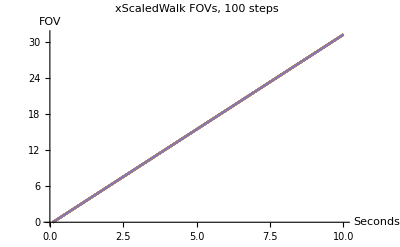

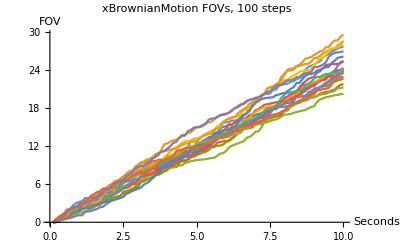

```mathematica
xPlotFOV[xProcess_,nSeconds_,iSteps_,iPaths_]:=Module[{vvnResultLists,vvnFOVLists,vnTimes},
vvnResultLists=Table[xProcess[nSeconds,iSteps],iPaths];
vnTimes=Rest[Range[0,nSeconds,nSeconds/iSteps]];
vvnFOVLists=Transpose[Table[xFOV[Take[#,x]]&/@vvnResultLists,{x,iSteps}]];
ListPlot[Transpose[{vnTimes,#}]&/@vvnFOVLists, Joined->True,ImageSize->400, PlotLabel->ToString[xProcess]<>" FOVs, "<>ToString[iSteps]<>" steps",AxesLabel->{Seconds,FOV}]
]

nSeconds=10;
iSteps=100;
iPaths=20;

xPlotFOV[xScaledWalk,nSeconds,iSteps,iPaths]
xPlotFOV[xBrownianMotion,nSeconds,iSteps,iPaths]
```

## Question 3b

The scaled random walk changes by c = ±1/(√(steps/seconds)) at every step, so its FOV increases constantly by |c| at each step. So, the FOV plot is the same for every scaled random walk path with the same number of seconds and steps. Brownian motion changes by a normal random value at each step. So, its FOV increases by a different value at each step. 
In this example, c = 1/(√10)=0.316 which is also the standard deviation of the Brownian motion √(seconds/steps). However, it is more likely for the the Brownian motion step to be in the range [-c,c] (68% of the normal distribution is within 1 standard deviation). So, the FOV is greater for the scaled random walk.

## Question 4

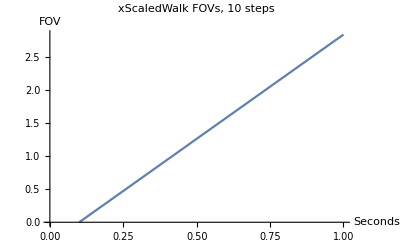
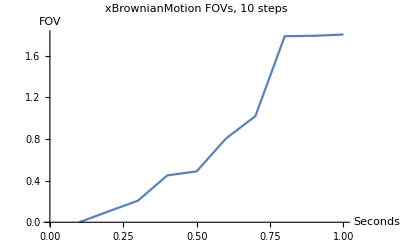

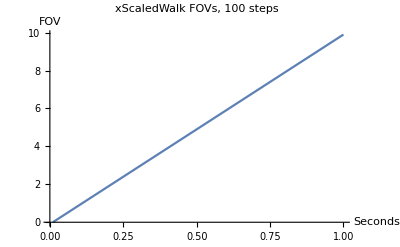
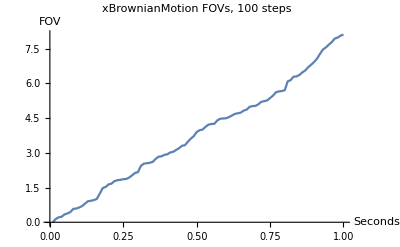

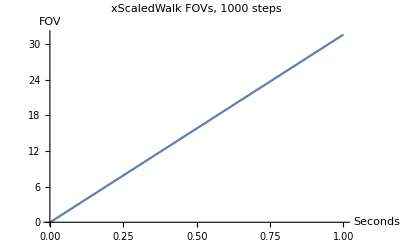
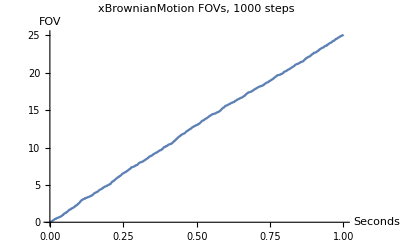

```mathematica
xDoQuestion4[nSeconds_,iSteps_,iPaths_]:=Module[{},
{xPlotFOV[xScaledWalk,nSeconds,iSteps,iPaths],
xPlotFOV[xBrownianMotion,nSeconds,iSteps,iPaths]}
]

nSeconds=1;
iPaths=1;

xDoQuestion4[nSeconds,10,iPaths]
xDoQuestion4[nSeconds,100,iPaths]
xDoQuestion4[nSeconds,1000,iPaths]
```

In the plots above for both the scaled random walk and Brownian motion, the number of seconds is held constant at 1 and the the number of steps is increased. So, the partition size decreases. It is clear that as the the partition size decreases, the FOV increases.